# Reconstructing exact stellar solutions for a quadratic model of gravity from a generic static, spherically symmetric interior metric

## Article ref: arXiv:2403.00070

Author: Mariam Campbell

Affiliation: University of Cape Town
Email: CMPMAR009@myuct.ac.za
Any enquiries about this file post 2025 can be sent to mariam.campbell09@gmail.com.

```mathematica
Quit[];
```

## Defining the metric

```mathematica
(* Defining our coordinates *)
X1={t,r,θ,ϕ};
(* Metric components *)
g={{1+D1 r^2+D2 r^4,0,0,0},{0,(1+D3 r^2)/(1+D4 r^2+D5 r^4),0,0},{0,0,r^2,0},{0,0,0,r^2Sin[θ]^2}}(* Metric g in comoving time *)
gup=Simplify[Inverse[g]];
```

{{1+D1 r^2+D2 r^4,0,0,0},{0,(1+D3 r^2)/(1+D4 r^2+D5 r^4),0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}}

```mathematica
(* The metric and inverse metric displayed in matrix form *)
MatrixForm[g]
MatrixForm[gup]
```

(1+D1 r^2+D2 r^4 | 0 | 0 | 0
0 | (1+D3 r^2)/(1+D4 r^2+D5 r^4) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

(1/(1+D1 r^2+D2 r^4) | 0 | 0 | 0
0 | (1+D4 r^2+D5 r^4)/(1+D3 r^2) | 0 | 0
0 | 0 | 1/r^2 | 0
0 | 0 | 0 | Csc[θ]^2/r^2)

```mathematica
(*The identity matrix: g^ab Subscript[g, ab]*)
gupdn=Table[Sum[gup[[a,c]]g[[c,b]],{c,1,4}],{a,1,4},{b,1,4}];
MatrixForm[%]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

## Defining the kinematics

```mathematica
(* The four-velocity: u^a*)
u={1/(√-g[[1,1]]),0,0,0}//PowerExpand 
(* Defining Subscript[u, a] *)
ud=Table[Sum[g[[aa,bb]]u[[bb]],{bb,1,4}],{aa,1,4}]
(* Computing u^a u^b Subscript[g, ab] *)
Sum[u[[aa]]u[[bb]]g[[aa,bb]],{aa,1,4},{bb,1,4}]
```

```mathematica
(* Defining the spatial vector: e^a *)
e={0,1/(√g[[2,2]]),0,0}//PowerExpand
(* Defining Subscript[e, a] *)
ed=Table[Sum[g[[aa,bb]]e[[bb]],{bb,1,4}],{aa,1,4}]//FullSimplify
(* Computing e^a e^b Subscript[g, ab] *)
Sum[e[[aa]]e[[bb]]g[[aa,bb]],{aa,1,4},{bb,1,4}]
```

```mathematica
(* The 3-dimensional metric Subscript[h, ab] *)
h=Table[g[[aa,bb]]+ud[[aa]]ud[[bb]],{aa,1,4},{bb,1,4}]
hup=Table[gup[[aa,bb]]+u[[aa]]u[[bb]],{aa,1,4},{bb,1,4}]
hdup=Table[Sum[h[[aa,bb]]gup[[bb,cc]],{bb,1,4}],{aa,1,4},{cc,1,4}]
(* The 2-dimensional metric Subscript[N, ab] *)
Nt=Table[g[[aa,bb]]+ud[[aa]]ud[[bb]]-ed[[aa]]ed[[bb]],{aa,1,4},{bb,1,4}]
Nup=Table[gup[[aa,bb]]+u[[aa]]u[[bb]]-e[[aa]]e[[bb]],{aa,1,4},{bb,1,4}]
Ndup=Table[Sum[Nt[[aa,bb]]gup[[bb,cc]],{bb,1,4}],{aa,1,4},{cc,1,4}]
```

{{1+D1 r^2+D2 r^4+((1+D1 r^2+D2 r^4)^2)/(-1-D1 r^2-D2 r^4),0,0,0},{0,(1+D3 r^2)/(1+D4 r^2+D5 r^4),0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}}

{{1/(-1-D1 r^2-D2 r^4)+1/(1+D1 r^2+D2 r^4),0,0,0},{0,(1+D4 r^2+D5 r^4)/(1+D3 r^2),0,0},{0,0,1/r^2,0},{0,0,0,Csc[θ]^2/r^2}}

{{(1+D1 r^2+D2 r^4+((1+D1 r^2+D2 r^4)^2)/(-1-D1 r^2-D2 r^4))/(1+D1 r^2+D2 r^4),0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

{{1+D1 r^2+D2 r^4+((1+D1 r^2+D2 r^4)^2)/(-1-D1 r^2-D2 r^4),0,0,0},{0,0,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}}

{{1/(-1-D1 r^2-D2 r^4)+1/(1+D1 r^2+D2 r^4),0,0,0},{0,0,0,0},{0,0,1/r^2,0},{0,0,0,Csc[θ]^2/r^2}}

{{(1+D1 r^2+D2 r^4+((1+D1 r^2+D2 r^4)^2)/(-1-D1 r^2-D2 r^4))/(1+D1 r^2+D2 r^4),0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
(* The 1+1+2 variables *)
CovDiffV[x_]:=Table[D[x[[aa]],X1[[bb]]]- Sum[Chr[[aa,bb,cc]]x[[cc]] ,{cc,1,4}],{aa,1,4}, {bb,1,4}]
Subϕ=ϕ-> Function[r, Evaluate[Sum[CovDiffV[ed][[aa,bb]]Nup[[aa,bb]],{aa,1,4}, {bb,1,4}]]]
Sub𝒜=𝒜 -> Function[r, Evaluate[Sum[CovDiffV[ud][[aa,bb]]u[[bb]]e[[aa]],{aa,1,4}, {bb,1,4}]]]//FullSimplify
ϕ[r]/.Subϕ//FullSimplify
𝒜[r]/.Sub𝒜//FullSimplify
```

ϕ→Function[r,(2 √(1+D4 r^2+D5 r^4))/(r √(1+D3 r^2))-((-2 D1 r-4 D2 r^3) √(1+D4 r^2+D5 r^4) (1/(-1-D1 r^2-D2 r^4)+1/(1+D1 r^2+D2 r^4)))/(2 √(1+D3 r^2))]

𝒜→Function[r,-((2 D1 r+4 D2 r^3) √(1+D4 r^2+D5 r^4))/(2 √(1+D3 r^2) (-1-D1 r^2-D2 r^4))]

(2 √(1+D4 r^2+D5 r^4))/(r √(1+D3 r^2))

(r (D1+2 D2 r^2) √(1+D4 r^2+D5 r^4))/(√(1+D3 r^2) (1+D1 r^2+D2 r^4))

## Christoffel Γ_mn^c, Riemann R_adf^b , Ricci R_ab and G_ab

```mathematica
(* Christoffel symbol Γ_mn^c, the first two indices are the lower one, the final index is the upper index. Ricci tensor is defined with two lower indices *)
Chr=Table[Sum[1/2*gup[[c,d]](D[g[[d,m]],X1[[n]]]+D[g[[n,d]],X1[[m]]]-D[g[[m,n]],X1[[d]]]),{d,1,4}],{m,1,4},{n,1,4},{c,1,4}];
(* Riemann tensor R_adf^b *)
Riemann=Table[
D[Chr[[aa,f,b]],X1[[d]]]-
D[Chr[[d,f,b]],X1[[aa]]]+
Sum[Chr[[d,s,b]]*Chr[[aa,f,s]],{s,1,4}]-
Sum[Chr[[aa,s,b]]*Chr[[d,f,s]],{s,1,4}],{aa,1,4},{d,1,4},{f,1,4},{b,1,4}];
Ricci=Table[Sum[Riemann[[aa,bb,cc,bb]],{bb,1,4}],{aa,1,4},{cc,1,4}];
```

```mathematica
(* Here we finally define the Ricci scalar and the Einstein tensor *)
Ricciscalar=Sum[gup[[q,b]]Ricci[[q,b]],{q,1,4},{b,1,4}]//FullSimplify
G=Simplify[Table[Ricci[[m,n]]-1/2*g[[m,n]]*Ricciscalar,{m,1,4},{n,1,4}]]
DrRicciscalar=D[Ricciscalar,r]//FullSimplify
```

1/((1+D3 r^2)^2 (1+D1 r^2+D2 r^4)^2)2 (-3 (D1-D3+D4)-(2 D1^2+10 D2+D3 (-D3+D4)+D1 (-4 D3+10 D4)+5 D5) r^2+(2 D1^2 (D3-3 D4)-2 D2 (D3+9 D4)-3 D3 D5-D1 (9 D2-2 D3^2+5 D3 D4+15 D5)) r^4-(6 D2^2+2 D2 (-D3^2+9 D1 D4+6 D3 D4+12 D5)+D1 (10 D3 D5+D1 (-D3^2+3 D3 D4+9 D5))) r^6-(D2 D3 (D2-2 D1 D3)+11 D2 (D2+D1 D3) D4+25 D1 D2 D5+6 (D1^2+3 D2) D3 D5) r^8+D2 (D2 D3 (D3-7 D4)-3 (5 D2+6 D1 D3) D5) r^10-11 D2^2 D3 D5 r^12)

{{((1+D1 r^2+D2 r^4) (3 D4-D3^2 r^2+5 D5 r^2+D3 (-3+D4 r^2+3 D5 r^4)))/((1+D3 r^2)^2),0,0,0},{0,(D4+4 D2 r^2+D5 r^2+5 D2 D4 r^4+5 D2 D5 r^6-D3 (1+D2 r^4)+D1 (2-D3 r^2+3 D4 r^2+3 D5 r^4))/((1+D1 r^2+D2 r^4) (1+D4 r^2+D5 r^4)),0,0},{0,0,1/((1+D3 r^2)^2 (1+D1 r^2+D2 r^4)^2)r^2 (D4+8 D2 r^2+2 D5 r^2+12 D2 D4 r^4+4 D2^2 r^6+16 D2 D5 r^6+7 D2^2 D4 r^8+10 D2^2 D5 r^10+D1^2 (r^2-(D3-3 D4) r^4+(D3 D4+5 D5) r^6+3 D3 D5 r^8)+D3 (-1+D5 r^4+D2^2 r^8 (1+4 D4 r^2+7 D5 r^4)+4 D2 (r^4+2 D4 r^6+3 D5 r^8))+D1 (2+5 D4 r^2+6 D2 r^4+8 D5 r^4+11 D2 D4 r^6+16 D2 D5 r^8+D3 r^2 (-1+2 D4 r^2+D2 r^4+5 D5 r^4+6 D2 D4 r^6+11 D2 D5 r^8))),0},{0,0,0,1/((1+D3 r^2)^2 (1+D1 r^2+D2 r^4)^2)r^2 (D4+8 D2 r^2+2 D5 r^2+12 D2 D4 r^4+4 D2^2 r^6+16 D2 D5 r^6+7 D2^2 D4 r^8+10 D2^2 D5 r^10+D1^2 (r^2-(D3-3 D4) r^4+(D3 D4+5 D5) r^6+3 D3 D5 r^8)+D3 (-1+D5 r^4+D2^2 r^8 (1+4 D4 r^2+7 D5 r^4)+4 D2 (r^4+2 D4 r^6+3 D5 r^8))+D1 (2+5 D4 r^2+6 D2 r^4+8 D5 r^4+11 D2 D4 r^6+16 D2 D5 r^8+D3 r^2 (-1+2 D4 r^2+D2 r^4+5 D5 r^4+6 D2 D4 r^6+11 D2 D5 r^8))) Sin[θ]^2}}

1/((1+D3 r^2)^3 (1+D1 r^2+D2 r^4)^3)4 r (4 D1^2+4 D1 D3-5 D3^2-4 D1 D4+5 D3 D4-5 (2 D2+D5)+(2 D1^3+2 D1^2 (7 D3-D4)-6 D2 (D3+4 D4)+D1 (4 D2+13 D3 (-D3+D4)-25 D5)-D3 (D3^2-D3 D4+D5)) r^2+3 (2 D1^3 D3+D2 (4 D2-5 D3 (D3+D4)-19 D5)+D1^2 (2 D2-3 D3^2+7 D3 D4-9 D5)+D1 (12 D2 D3-D3^3-8 D2 D4+D3^2 D4-5 D3 D5)) r^4-(3 D1^3 (D3^2-3 D3 D4+3 D5)+D2 (-44 D2 D3+3 D3^3+8 D2 D4+7 D3^2 D4+65 D3 D5)+D1^2 (6 D2 (-4 D3+D4)+D3 (3 D3^2-7 D3 D4+13 D5))+2 D1 (-6 D2^2+2 D3^2 D5+D2 (5 D3^2-11 D3 D4+47 D5))) r^6-(-6 D2^3+D1 D2 D3 (5 D1 D3+6 D3^2-23 D1 D4-10 D3 D4)+D2 (41 D1^2+82 D1 D3+24 D3^2) D5+D2^2 (4 D1 (-10 D3+D4)-9 D3 (D3+3 D4)+51 D5)+D1^2 D3 (2 D3 D5+D1 (D3^2-3 D3 D4+3 D5))) r^8-3 D2 (-6 D2^2 D3+D1 D3 (8 D3 D5+D1 (D3^2-3 D3 D4+9 D5))+D2 (-D1 D3 (D3+11 D4)+15 D1 D5+D3 (D3^2-5 D3 D4+13 D5))) r^10+D2 (3 D2^2 (D3^2+5 D3 D4-5 D5)-6 D1^2 D3^2 D5-D2 D3 (8 D3 D5+3 D1 (D3^2-5 D3 D4+9 D5))) r^12-D2^2 D3 (4 D1 D3 D5+D2 (D3^2-7 D3 D4+7 D5)) r^14)

## The energy momentum tensor, T_ab, in the (1+1+2) threading

```mathematica
T=Table[ρ[t] ud[[aa]]ud[[bb]]+(p[t]-1/2 Π[t]) Nt[[aa,bb]]+(p[t]+Π[t])ed[[aa]]ed[[bb]],{aa,1,4},{bb,1,4}]//FullSimplify
Tupdn=Table[Sum[gup[[nn,aa]]T[[nn,bb]], {nn,1,4}],{aa,1,4},{bb,1,4}]//FullSimplify
```

{{-((1+D1 r^2+D2 r^4) ρ[t]),0,0,0},{0,((1+D3 r^2) (p[t]+Π[t]))/(1+D4 r^2+D5 r^4),0,0},{0,0,r^2 (p[t]-Π[t]/2),0},{0,0,0,r^2 Sin[θ]^2 (p[t]-Π[t]/2)}}

{{-ρ[t],0,0,0},{0,p[t]+Π[t],0,0},{0,0,p[t]-Π[t]/2,0},{0,0,0,p[t]-Π[t]/2}}

## Using junction conditions to reduce number of parameter dependence

```mathematica
SubJunc=Solve[{Ricciscalar==0,DrRicciscalar==0,G[[2,2]]==0},{D3,D4, D5}]/.r-> rs
```

{{D3→(3 (5 D1+13 D1^2 rs^2+10 D2 rs^2+12 D1^3 rs^4+30 D1 D2 rs^4+49 D1^2 D2 rs^6+61 D1 D2^2 rs^8+30 D2^3 rs^10))/(rs^2 (-3 D1+3 D1^2 rs^2-22 D2 rs^2+14 D1 D2 rs^4+3 D1^2 D2 rs^6+72 D2^2 rs^6+37 D1 D2^2 rs^8+22 D2^3 rs^10)),D4→(15 D1+72 D1^2 rs^2+30 D2 rs^2+75 D1^3 rs^4+287 D1 D2 rs^4+36 D1^4 rs^6+320 D1^2 D2 rs^6+230 D2^2 rs^6+207 D1^3 D2 rs^8+129 D1 D2^2 rs^8+284 D1^2 D2^2 rs^10-310 D2^3 rs^10+41 D1 D2^3 rs^12-30 D2^4 rs^14)/(rs^2 (-3 D1-6 D1^2 rs^2-22 D2 rs^2+9 D1^3 rs^4-67 D1 D2 rs^4+60 D1^2 D2 rs^6-38 D2^2 rs^6+9 D1^3 D2 rs^8+323 D1 D2^2 rs^8+126 D1^2 D2^2 rs^10+382 D2^3 rs^10+251 D1 D2^3 rs^12+110 D2^4 rs^14)),D5→-((2 (6 D1^2+3 D1^3 rs^2+48 D1 D2 rs^2+42 D1^2 D2 rs^4+56 D2^2 rs^4+15 D1^3 D2 rs^6+28 D1 D2^2 rs^6+20 D1^2 D2^2 rs^8-56 D2^3 rs^8-20 D1 D2^3 rs^10-16 D2^4 rs^12))/(rs^2 (-3 D1-6 D1^2 rs^2-22 D2 rs^2+9 D1^3 rs^4-67 D1 D2 rs^4+60 D1^2 D2 rs^6-38 D2^2 rs^6+9 D1^3 D2 rs^8+323 D1 D2^2 rs^8+126 D1^2 D2^2 rs^10+382 D2^3 rs^10+251 D1 D2^3 rs^12+110 D2^4 rs^14)))}}

## Fluid quantities in terms of the aerial radius r

```mathematica
Clear[R,f]
```

```mathematica
(* Starobinsky *)
Subf=f-> Function[R,R+α*R^2];
f[R[r]]/.Subf
```

R[r]+α R[r]^2

```mathematica
Simplify[f'[R[r]]/.Subf/.R-> Function[r,Evaluate[Ricciscalar]]/.SubJunc/.r->rs]
```

{1}

```mathematica
μRgen=Simplify[R[k]/2-f[R[k]]/(2 f'[R[k]])+(ϕ[k]^2 R'[k] f''[R[k]])/f'[R[k]]+(ϕ[k] R'[k] ϕ'[k] f''[R[k]])/f'[R[k]]+(ϕ[k]^2 f''[R[k]] R''[k])/f'[R[k]]+(ϕ[k]^2 R'[k]^2 Derivative[3][f][R[k]])/f'[R[k]]/.R''[k]->1/2 r*D[1/2 r*R'[r],r]/.R'[k]->1/2 r*R'[r]/.ϕ'[k]->1/2 r*ϕ'[r]/.k->r];
pRgen=Simplify[-R[k]/2+f[R[k]]/(2 f'[R[k]])-(𝒜[k] ϕ[k] R'[k] f''[R[k]])/f'[R[k]]-(2 ϕ[k]^2 R'[k] f''[R[k]])/(3 f'[R[k]])-(2 ϕ[k] R'[k] ϕ'[k] f''[R[k]])/(3 f'[R[k]])-(2 ϕ[k]^2 f''[R[k]] R''[k])/(3 f'[R[k]])-(2 ϕ[k]^2 R'[k]^2 Derivative[3][f][R[k]])/(3 f'[R[k]])/.R''[k]->1/2 r*D[1/2 r*R'[r],r]/.R'[k]->1/2 r*R'[r]/.ϕ'[k]->1/2 r*ϕ'[r]/.k->r];
ΠRgen=Simplify[-(ϕ[k]^2 R'[k] f''[R[k]])/(3 f'[R[k]])+(2 ϕ[k] R'[k] ϕ'[k] f''[R[k]])/(3 f'[R[k]])+(2 ϕ[k]^2 f''[R[k]] R''[k])/(3 f'[R[k]])+(2 ϕ[k]^2 R'[k]^2 Derivative[3][f][R[k]])/(3 f'[R[k]])/.R''[k]->1/2 r*D[1/2 r*R'[r],r]/.R'[k]->1/2 r*R'[r]/.ϕ'[k]->1/2 r*ϕ'[r]/.k->r];
```

```mathematica
μR=Simplify[μRgen/.Subf/.Subϕ/.R-> Function[r,Evaluate[Ricciscalar]]];
pR=Simplify[pRgen/.Subf/.Subϕ/.Sub𝒜/.R-> Function[r,Evaluate[Ricciscalar]]];
ΠR=Simplify[ΠRgen/.Subf/.Subϕ/.Sub𝒜/.R-> Function[r,Evaluate[Ricciscalar]]];
```

```mathematica
pRrad=(pR+ΠR);
pRperp=(pR-1/2 ΠR);
```

```mathematica
Simplify[pRrad/.SubJunc/.r->rs]
```

{0}

```mathematica
μm=Simplify[(-1/(1+D1*r^2+D2*r^4)G[[1,1]]-μR)*f'[R[r]]/.Subf/.R-> Function[r,Evaluate[Ricciscalar]]];
pmrad=Simplify[(((1+D3*r^2)/(1+D4*r^2+D5*r^4))^-1 G[[2,2]]-pRrad)*f'[R[r]]/.Subf/.R-> Function[r,Evaluate[Ricciscalar]]];
pmperp=Simplify[(r^-2 G[[3,3]]-pRperp)*f'[R[r]]/.Subf/.R-> Function[r,Evaluate[Ricciscalar]]];
```

```mathematica
Simplify[pmrad/.SubJunc/.r->rs]
```

{0}

```mathematica
SubPar={α->0.0001, D1->6.8, D2->10,rs->1};
SubPar2={α->0.0235, D1->6.8, D2->10,rs->1};
SubPar3={α->0.0394, D1->6.8, D2->10,rs->1};
SubPar4={α->0.00015, D1->6.8, D2->10,rs->1};
SubPar5={α->0.0002, D1->6.8, D2->10,rs->1};
```

```mathematica
c2mr=(D[pmrad,r]/D[μm,r])/.SubJunc;
c2mperp=(D[pmperp,r]/D[μm,r])/.SubJunc;
```

```mathematica
X=((r/2)*(ϕ[r]/.Subϕ)*D[Ricciscalar,r]/.SubJunc[[1]])//Simplify;
```

```mathematica
Limit[c2mperp/.SubPar,r->0]
```

{0.926311}

```mathematica
Limit[c2mr/.SubPar,r->0]
```

{0.790565}

```mathematica
{c2mr,c2mperp}/.SubPar4;
Plot[%,{r,0,1.01},PlotRange->{-0.1,1.1},AxesOrigin->{0,0},GridLines->{{1},{0,1}},GridLinesStyle->Directive[Gray, Dashed],PlotTheme->"Scientific",PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotLegends->Placed[LineLegend[{"(c^2)_(m,  r)","(c^2)_(m,   ⊥)"},LegendFunction->"Frame",LabelStyle->{FontSize->20,FontFamily->"Times"}],{1,0.89}],LabelStyle->{FontSize->30,FontFamily->"Times"},Frame->{{True,True},{True,True}},FrameLabel->{r,""},ImageSize->Scaled[1.],PlotLabel->"α=0.00015"]
```

-Graphics-

```mathematica
{c2mr,c2mperp}/.SubPar;
Plot[%,{r,0,1.01},PlotRange->{-0.1,1.1},AxesOrigin->{0,0},GridLines->{{1},{0,1}},GridLinesStyle->Directive[Gray, Dashed],PlotTheme->"Scientific",PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotLegends->Placed[LineLegend[{"(c^2)_(m,  r)","(c^2)_(m,   ⊥)"},LegendFunction->"Frame",LabelStyle->{FontSize->20,FontFamily->"Times"}],{1,0.89}],LabelStyle->{FontSize->30,FontFamily->"Times"},Frame->{{True,True},{True,True}},FrameLabel->{r,""},ImageSize->Scaled[1.],PlotLabel->"α=0.0001"]
```

-Graphics-

```mathematica
p1=c2mr/.SubPar;p2=c2mperp/.SubPar;p3=c2mr/.SubPar5;p4=c2mperp/.SubPar5;
Plot[{0.1,p1,p2,0.1,p3,p4},{r,0,1.01},PlotRange->{-0.1,1.1},AxesOrigin->{0,0},GridLines->{{1},{0,1}},GridLinesStyle->Directive[Gray, Dashed],PlotTheme->"Scientific",PlotStyle->{White,Thickness[0.005],Thickness[0.005],White,{Dashed,Thickness[0.005]},{Dashed,Thickness[0.005]}},PlotLegends->Placed[LineLegend[{"α=0.0001:","(c^2)_(m,  r)","(c^2)_(m,   ⊥)","α=0.0002:","(c^2)_(m,  r)","(c^2)_(m,   ⊥)"},LegendFunction->"Frame",LabelStyle->{FontSize->20,FontFamily->"Times"}],{1,0.7}],LabelStyle->{FontSize->30,FontFamily->"Times"},Frame->{{True,True},{True,True}},FrameLabel->{r,""},ImageSize->Scaled[1.]]
```

-Graphics-

```mathematica
{pmrad/.SubJunc,pRrad/.SubJunc,Ricciscalar/.SubJunc,X,pmperp/.SubJunc,μm/.SubJunc}/.SubPar;
Plot[%,{r,0,1.01},PlotRange->All,AxesOrigin->{0,0},GridLines->{{1},{0}},GridLinesStyle->Directive[Gray, Dashed],PlotTheme->"Scientific",PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotLegends->Placed[LineLegend[{"(p^m)_r","(p^R)_r","R","R̂","(p^m)_⊥","μ^m"},LegendFunction->"Frame",LabelStyle->{FontSize->20,FontFamily->"Times"}],{1,0.7}],LabelStyle->{FontSize->30,FontFamily->"Times"},Frame->{{True,True},{True,True}},FrameLabel->{r,""},ImageSize->Scaled[1.]]
```

```mathematica
{pmrad/.SubJunc,pRrad/.SubJunc,Ricciscalar/.SubJunc,X,pmperp/.SubJunc,μm/.SubJunc}/.SubPar5;
Plot[%,{r,0,1.01},PlotRange->All,AxesOrigin->{0,0},GridLines->{{1},{0}},GridLinesStyle->Directive[Gray, Dashed],PlotTheme->"Scientific",PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotLegends->Placed[LineLegend[{"(p^m)_r","(p^R)_r","R","R̂","(p^m)_⊥","μ^m"},LegendFunction->"Frame",LabelStyle->{FontSize->20,FontFamily->"Times"}],{1,0.7}],LabelStyle->{FontSize->30,FontFamily->"Times"},Frame->{{True,True},{True,True}},FrameLabel->{r,""},ImageSize->Scaled[1.]]
```

-Graphics-

```mathematica
{pmrad/.SubJunc,pmperp/.SubJunc,μm/.SubJunc}/.SubPar;
Plot[%,{r,0,1.01},PlotRange->All,AxesOrigin->{0,0},GridLines->{{1},{0}},GridLinesStyle->Directive[Gray, Dashed],PlotTheme->"Scientific",PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotLegends->Placed[LineLegend[{"(p^m)_r","(p^m)_⊥","μ^m"},LegendFunction->"Frame",LabelStyle->{FontSize->20,FontFamily->"Times"}],{1.,0.93}],LabelStyle->{FontSize->30,FontFamily->"Times"},Frame->{{True,True},{True,True}},FrameLabel->{r,""},ImageSize->Scaled[1.]]
```

-Graphics-

```mathematica
{pmrad/.SubJunc,pmperp/.SubJunc,μm/.SubJunc}/.SubPar5;
Plot[%,{r,0,1.01},PlotRange->All,AxesOrigin->{0,0},GridLines->{{1},{0}},GridLinesStyle->Directive[Gray, Dashed],PlotTheme->"Scientific",PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotLegends->Placed[LineLegend[{"(p^m)_r","(p^m)_⊥","μ^m"},LegendFunction->"Frame",LabelStyle->{FontSize->20,FontFamily->"Times"}],{1.,0.93}],LabelStyle->{FontSize->30,FontFamily->"Times"},Frame->{{True,True},{True,True}},FrameLabel->{r,""},ImageSize->Scaled[1.]]
```

-Graphics-

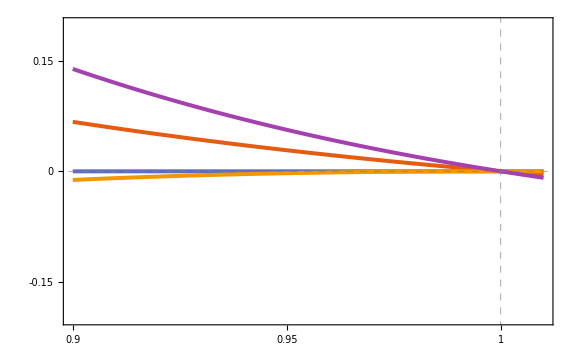

```mathematica
{pmrad/.SubJunc,pRrad/.SubJunc,Ricciscalar/.SubJunc,X,pmperp/.SubJunc,μm/.SubJunc}/.SubPar;
Plot[%,{r,0.9,1.01},PlotRange->{-0.2,0.2},GridLines->{{1},{0,1}},GridLinesStyle->Directive[Gray, Dashed],PlotTheme->"Scientific",PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},LabelStyle->{FontSize->20,FontFamily->"Times"},Frame->{{True,True},{True,True}},FrameLabel->{"",""},FrameTicks->{{{-0.15,0,0.15},None},{{0.9,0.95,1},None}},ImageSize->Large]
```

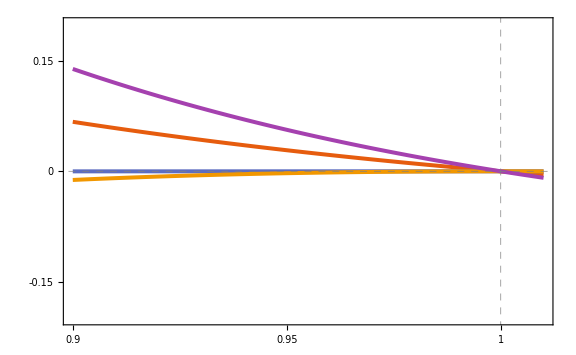

```mathematica
{pmrad/.SubJunc,pRrad/.SubJunc,Ricciscalar/.SubJunc,X,pmperp/.SubJunc,μm/.SubJunc}/.SubPar5;
Plot[%,{r,0.9,1.01},PlotRange->{-0.2,0.2},GridLines->{{1},{0,1}},GridLinesStyle->Directive[Gray, Dashed],PlotTheme->"Scientific",PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},LabelStyle->{FontSize->20,FontFamily->"Times"},Frame->{{True,True},{True,True}},FrameLabel->{"",""},FrameTicks->{{{-0.15,0,0.15},None},{{0.9,0.95,1},None}},ImageSize->Large]
```

```mathematica
{pRrad/.SubJunc,pRperp/.SubJunc,μR/.SubJunc}/.SubPar;
Plot[%,{r,0,1.01},PlotRange->All,AxesOrigin->{0,0},GridLines->{{1},{0}},GridLinesStyle->Directive[Gray, Dashed],PlotTheme->"Scientific",PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotLegends->Placed[LineLegend[{"(p^R)_r","(p^R)_⊥","μ^R"},LegendFunction->"Frame",LabelStyle->{FontSize->20,FontFamily->"Times"}],{1,0.84}],LabelStyle->{FontSize->30,FontFamily->"Times"},Frame->{{True,True},{True,True}},FrameLabel->{r,""},ImageSize->Scaled[1.]]
```

-Graphics-

## Checks...

```mathematica
(* Checking if the total quantities derived from the reconstruction method subtracted from the total quantities computed directly from the field equations results in zero *)
```

```mathematica
FullSimplify[-1/(1+D1*r^2+D2*r^4)G[[1,1]]-(-3 D4+D3^2 r^2-5 D5 r^2-D3 (-3+D4 r^2+3 D5 r^4))/((1+D3 r^2)^2)]
FullSimplify[((1+D3*r^2)/(1+D4*r^2+D5*r^4))^-1 G[[2,2]]-(D4+4 D2 r^2+D5 r^2+5 D2 D4 r^4+5 D2 D5 r^6-D3 (1+D2 r^4)+D1 (2-D3 r^2+3 D4 r^2+3 D5 r^4))/((1+D3 r^2) (1+D1 r^2+D2 r^4))]
FullSimplify[r^-2 G[[3,3]]-(1/((1+D3 r^2)^2 (1+D1 r^2+D2 r^4)^2)(D4+8 D2 r^2+2 D5 r^2+12 D2 D4 r^4+4 D2^2 r^6+16 D2 D5 r^6+7 D2^2 D4 r^8+10 D2^2 D5 r^10+D1^2 (r^2-(D3-3 D4) r^4+(D3 D4+5 D5) r^6+3 D3 D5 r^8)+D3 (-1+D5 r^4+D2^2 r^8 (1+4 D4 r^2+7 D5 r^4)+4 D2 (r^4+2 D4 r^6+3 D5 r^8))+D1 (2+5 D4 r^2+6 D2 r^4+8 D5 r^4+11 D2 D4 r^6+16 D2 D5 r^8+D3 r^2 (-1+2 D4 r^2+D2 r^4+5 D5 r^4+6 D2 D4 r^6+11 D2 D5 r^8))))]
```